```mathematica
ClearAll["Global`*"];
orthog[m_,n_]:=
Module[{nn=n,mm=m,σ,a,b,Ja,w,xi,eval,evec,esys},
σ=Table[0.,{i,1,2nn},{j,1,2nn}];
Do[σ[[2,i+1]]=mm[[i+1]],{i,0,2nn-1}];

a=Table[0.,{i,1,nn}];b=a;
a[[1]]=mm[[2]]/mm[[1]];
b[[1]]=0;

Do[
Do[
σ[[i+2,j+1]]=σ[[i+1,j+2]]-a[[i]]σ[[i+1,j+1]]-b[[i]]σ[[i,j+1]];
a[[i+1]]=-σ[[i+1,i+1]]/σ[[i+1,i]]+σ[[i+2,i+2]]/σ[[i+2,i+1]];
b[[i+1]]=σ[[i+2,i+1]]/σ[[i+1,i]];
,{j,i,2nn-i-1}];
,{i,1,nn-1}];

Ja=DiagonalMatrix[a];
Do[
Ja[[i,i+1]]=-Sqrt[Abs[b[[i+1]]]];
Ja[[i+1,i]]=-Sqrt[Abs[b[[i+1]]]];
,{i,1,nn-1}];

esys=Eigensystem[Ja];
eval=esys[[1]];evec=esys[[2]];

w=Table[evec[[i,1]]^2 mm[[1]],{i,1,nn}];
{eval,w}
];
```

```mathematica
(* Physical parameters *)
(*Ca=1;
Cp=-1;
γ=1;Rey=10 10^6;*)
(*γ=1/2;Rey=4;*)
Ca=1;Cp=0;γ=1;Rey=Infinity;

μR=1.;
σR=0.1;
μRd=0.1;
σRd=0.1;
ρRRd=0.0;
RRdPDF=BinormalDistribution[{μR,μRd},{σR,σRd},ρRRd ];
momRRd[i_,j_]:=Moment[RRdPDF,{i,j}];

nr=4;
nrd=4;
ks=Flatten[{Table[{q,p},{q,0,nr-1},{p,0,2nrd-1}],
Table[{q,p},{q,nr,2nr-1},{p,0,0}]}
,2];

myrhs[momin_]:=
Module[{moms=momin,rhs},
(* converts vector of total M_lmn to M_lm @ each R_o,k *)
eqns=Table[moms[[i]]==pm[ks[[i,1]],ks[[i,2]]],{i,1,Length[ks]}];
vars=DeleteDuplicates[Flatten[Table[pm[ks[[i,1]],ks[[i,2]]],{i,1,Length[ks]}]]];
linsolv=First[vars/.Solve[eqns,vars]];
(* conditioned moments *)
mymom[q_,p_]:=linsolv[[First[First[Position[ks,{q,p}]]]]];

(* get conditional moments *)
mRs=Table[mymom[i,0],{i,0,2nr-1}];
{xi,w}=orthog[mRs,nr];
If[Min[w]<10^-12,Print["Negative weight, w = ",w];Abort[];];
v=Table[
Table[xi[[i]]^j,{i,1,nr}]
,{j,0,nr-1}];
r1=DiagonalMatrix[w];
Do[ms[m]=Table[mymom[i,m],{i,0,nr-1}],{m,0,2nrd-1}];
Do[condmoms[i]=LinearSolve[v.r1,ms[i]],{i,0,2nrd-1}];
Do[condmomvec[j]=Table[condmoms[i][[j]],{i,0,2nrd-1}];,{j,1,nr}];
Do[
{xis[i],ws[i]}=orthog[condmomvec[i],nrd];
,{i,1,nr}];
Do[
wtot[j,i]=w[[j]]ws[j][[i]];
If[ws[j][[i]]<10^-12,Print["Negative weight, ws = ",ws[j]," abscissa = ",xis[j]];Abort[];];
,{i,1,nrd},{j,1,nr}];

(* note that in mom[p,q,l], l is the Ro index and p and q are moment exponents! *)
mom[p_,q_]:=Sum[wtot[j,i] xi[[j]]^p(xis[j][[i]])^q,{i,1,nrd},{j,1,nr}];
(* turns conditional moments into total moments *)
momtot[p_,q_]:=mom[p,q];

rhs={};
Do[
l=ks[[i,1]];
m=ks[[i,2]];
AppendTo[rhs,
l momtot[l-1,m+1]-m(4/Rey momtot[l,m]+2 γ Ca momtot[l+1,m-1]+Cp momtot[l,m-1])];
,{i,1,Length[ks]}];
rhs
];
```

```mathematica
dt0=1  10^-4;
dt=dt0;
dtmin=dt 0.0001;
(*Nt=10000;*)
T=10;
tol=1 10^-4;

(* gets total moments in {lmn} from conditional moments on {lm} plus Ro directions *)
ic=Table[momRRd[ks[[i,1]],ks[[i,2]]],{i,1,Length[ks]}];
moms=ic;

sol={};ts={};dets={};
t=0;
Monitor[While[t≤T,
AppendTo[sol,moms];
AppendTo[ts,t];
rhs1=myrhs[moms];
mome=moms+dt rhs1;

(* RK2 *)
(*momstemp1=moms+dt/2 rhs1;
moms=moms+dt myrhs[momstemp1];*)

(* Four-stage RK3 *)
momstemp1=1/2 moms+1/2(moms+dt rhs1);
momstemp2=1/2 momstemp1+1/2(momstemp1+dt myrhs[momstemp1]);
momstemp3=2/3 moms+1/6 momstemp2+1/6(momstemp2+dt myrhs[momstemp2]);
moms=1/2 momstemp3+1/2(momstemp3+dt myrhs[momstemp3]);

e=Norm[moms-mome,1];

(*mydet={};
Do[
hm=Table[0,{i,1,nrd},{j,1,nrd}];
Do[hm[[i,j]]=condmomvec[k][[i+j]],{i,1,nrd},{j,1,nrd}];
AppendTo[mydet,Det[hm]];
,{k,1,nr}];
AppendTo[dets,mydet];*)

mydet={};
(* conditional moment sets *)
(*Do[
Do[
Do[
hm=Table[0,{i,1,nrd-l},{j,1,nrd-l}];
Do[hm[[i,j]]=condmomvec[k][[i+j-p]],{i,1,nrd-l},{j,1,nrd-l}];
det=Det[hm];
If[det>0,
AppendTo[mydet,det],
Print["Unrealizable mom set ",det," ",condmomvec[k]];
Abort[];
];
,{l,0,nrd-2}];
,{p,0,1}];
,{k,1,nr}];*)

(* un-conditioned moment set *)
Do[
l=0;
(*Do[*)
hm=Table[0,{i,1,nr-l},{j,1,nr-l}];
Do[hm[[i,j]]=mRs[[i+j-p]],{i,1,nr-l},{j,1,nr-l}];
det=Det[hm];
AppendTo[mydet,det];
(*If[det<0,
Print["Unrealizable mom set ",det," ",mRs," l = ",l," p = ",p," matrix = ",MatrixForm[hm]," w ",w];
Abort[];
];*)
(*,{l,0,nr-2}];*)
,{p,0,1}];
AppendTo[dets,mydet];

If[Norm[moms]>10^3,
Print["Crash ",100 t/T];
Break[];
];
t=t+dt;
dt=Max[0.9 dt Min[Max[Sqrt[tol/(2 e)],0.3],2.],dtmin];
];
,{100t/T,dt/dt0}
];
```

{0.,-2.,-0.4,-0.12,-0.032,-0.01,-0.00312,-0.001064,0.1,-2.,-0.4,-0.1202,-0.03206,-0.010024,-0.003128,-0.00106724,0.2,-2.02,-0.404,-0.1216,-0.03244,-0.010148,-0.0031672,-0.00108112,0.303,-2.06,-0.412,-0.124206,-0.0331418,-0.0103727,-0.00323784,-0.00110574,0.412,0.53015,0.6609,0.80816}

$Aborted

```mathematica
idx=1;
condmomvec[idx]
orthog[condmomvec[idx],nrd]
```

{1.,-1.44819,2.11677,-3.12202,4.6452,-6.97067,10.5469,-16.0848}

{{-17.6267,-1.64082,-1.38243,-1.0866},{8.55959×10^-13,0.302322,0.655918,0.0417605}}

{{-1.58789,-1.3085},{0.499999,0.500001}}

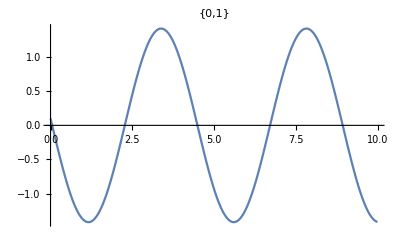
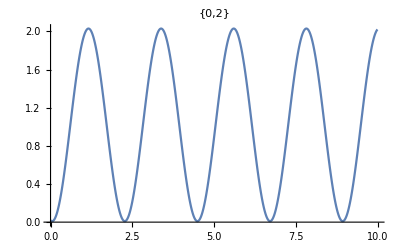
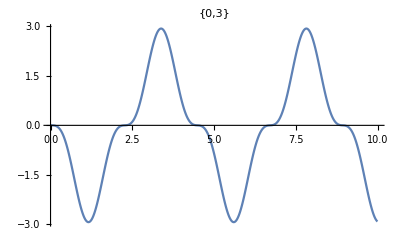
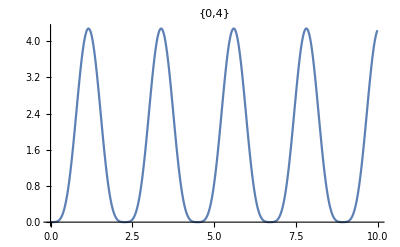
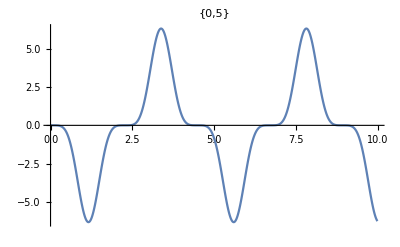
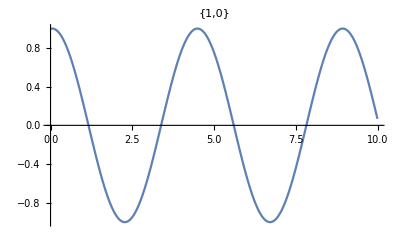
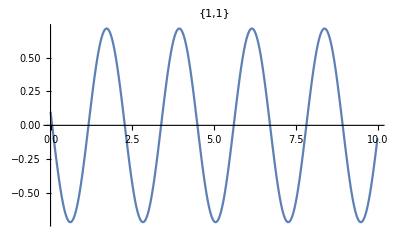
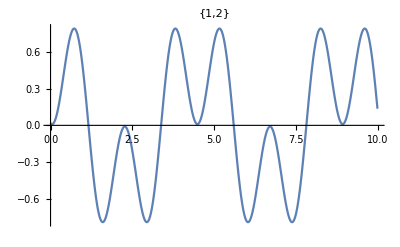

```mathematica
plots={};
Do[
If[Total[ks[[i]]]<10&&Total[ks[[i]]]>0,
AppendTo[plots,ListPlot[Thread[{ts,sol[[All,i]]}],Joined->True,PlotRange->All,PlotLabel->ks[[i]]]]
]
,{i,1,Length[moms]}]
plots
```

```mathematica
hm//MatrixForm
```

(1. | 0.0653873
0.0653873 | 0.00927595)

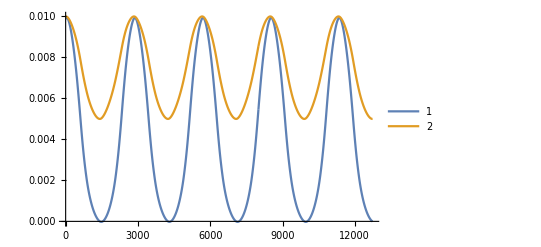

-Graphics-

```mathematica
ListPlot[Table[dets[[All,i]],{i,1,Length[dets[[1]]]}],Joined->True,PlotRange->All,PlotLegends->Automatic]
```

```mathematica
(* hankel-hadamard matrix for nr =2, nrd = 3 *)
(*hm=Table[0,{i,1,2nrd},{j,1,2nrd}];
Do[condmomvec[j]=Table[condmoms[i][[j]],{i,0,2nrd-1}];,{j,1,nr}];*)

Lmom=2nrd-1;
Lside=(Lmom+1)/2;

(* conditional moment sets *)
Do[
Do[
Do[
hm=Table[0,{i,1,nrd-l},{j,1,nrd-l}];
Do[hm[[i,j]]=condmomvec[k][[i+j-p]],{i,1,nrd-l},{j,1,nrd-l}];
Print[k," ",l," ",p," ",Det[hm]];
,{l,0,nrd-2}];
,{p,0,1}];
,{k,1,nr}];
(* un-conditioned moment set *)

Do[
Do[
hm=Table[0,{i,1,nr-l},{j,1,nr-l}];
Do[hm[[i,j]]=mRs[[i+j-p]],{i,1,nr-l},{j,1,nr-l}];
Print[l," ",p," ",Det[hm]];
,{l,0,nr-2}];
,{p,0,1}];
```

1 0 0 0.00764097

1 1 0 0.186665

1 0 1 0.0312499

1 1 1 0.25

2 0 0 0.00774953

2 1 0 0.187052

2 0 1 0.0312501

2 1 1 0.25

3 0 0 0.00785855

3 1 0 0.18744

3 0 1 0.03125

3 1 1 0.25

0 0 0.00787552

1 0 0.187948

0 1 0.0312499

1 1 0.25

```mathematica
mRs
```

{1.,1.0009,1.25179,1.75336,2.69377,4.44954}

```mathematica
Det[hm]
```

0.18744

```mathematica
condmomvec[nr]
```

{1.,-0.409778,0.655969,-0.668781,1.02051,-1.08654}

```mathematica
hm//MatrixForm
```

(-0.409778 | 0.655969 | -0.668781
0.655969 | -0.668781 | 1.02051
-0.668781 | 1.02051 | -1.08654)

```mathematica
Ncases=1000;
cases=RandomVariate[BinormalDistribution[{μR[1],μRd[1]},{σR[1],σRd[1]},ρRRd[1]],Ncases];
R0=μRo;
Nt=100;
β=2/(Rey R0^2);
ω2=(2 γ Ca)/R0^2;
Clear[t];
linmyr=ParallelTable[
r[t]/.(NDSolve[
{r''[t] == -2 β r'[t]-ω2 r[t]-Cp/R0,r[0]==cases[[i,1]],r'[0]==cases[[i,2]]},
r[t],
{t,0,T}]//First//First),
{i,1,Ncases}];
linmydr=Table[
D[linmyr[[i]],t],{i,1,Ncases}];

ts2=Table[i,{i,0,T,T/Nt}];
Nt=Length[ts2];
Plin=Table[Table[{
linmyr[[j]]/.{t->ts2[[i]]},
linmydr[[j]]/.{t->ts2[[i]]}},{j,1,Ncases}],
{i,1,Nt}];

nonlinmoments=Table[Table[{ts2[[i]],Moment[Plin[[i]],ks[[j,1;;2]]]},{i,1,Nt}],{j,1,Length[ks]}];
```

```mathematica
ks[[All,1;;2]]
```

{{0,0},{0,1},{0,2},{0,3},{1,0},{1,1},{1,2},{1,3},{2,0},{3,0}}

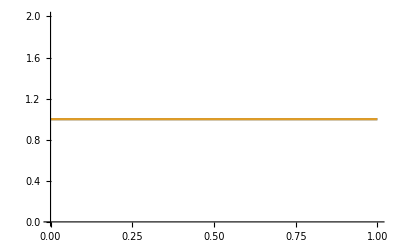
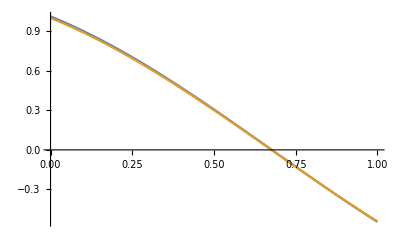
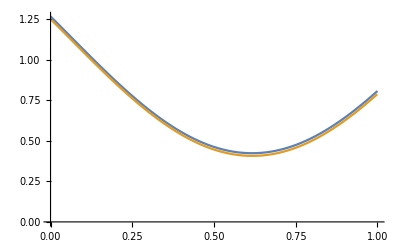
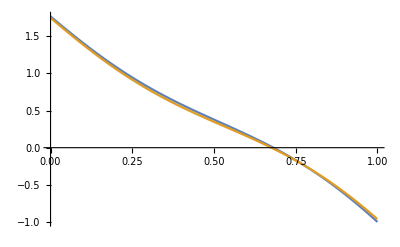
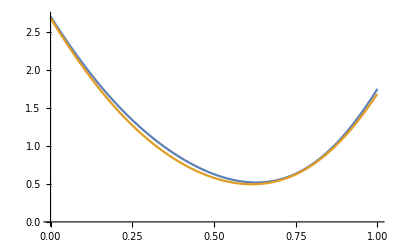
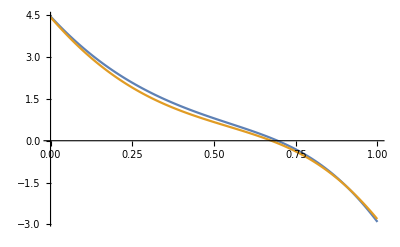
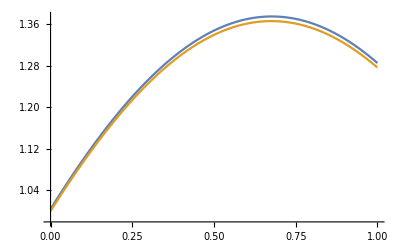
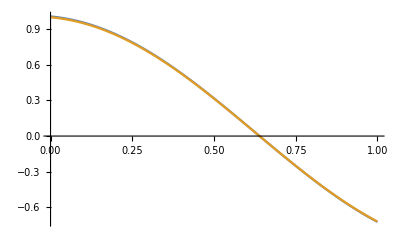

```mathematica
Table[ListPlot[{nonlinmoments[[i]],Thread[{ts,sol[[All,i]]}]},PlotRange->All,Joined->True],{i,1,Length[ks]}]
```